```mathematica
ClearAll["Global`*"]
```

```mathematica
scientstring[n_,dig_]:=ToString[ScientificForm[n,dig],TraditionalForm]
```

```mathematica
Trapz[x_,y_]:=Total@Table[{((y[[i]]+y[[i+1]])Abs@(x[[i+1]]-x[[i]]))/2},{i,1,Length@x-1}]//Flatten
CumTrapz[x_,y_]:=Module[{areas,cumarea},
areas=Table[{((y[[i]]+y[[i+1]])Abs@(x[[i+1]]-x[[i]]))/2},{i,1,Length@x-1}];cumarea=0;Table[cumarea=cumarea+areas[[i]],{i,1,Length@areas}]]//Flatten
```

```mathematica
LinSpace[s_,f_,n_]:=Range[s,f,(f-s)/(n-1)]
```

```mathematica
alldata=Import["ovalcell_data.m"]
```

<|cellVal→{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,w0→1/10,tp0→1/40000,tf0→1/100000,ϵ1max→0.05},tankVal→{d→5,Pt→50000,Vtank→1,Vftot→1,f→0.1},gasVal→{patm→101325,Tstd→288.15,γair→1.4,ρstdair→1.225,cv→717.2,cp→1.0042}|>

```mathematica
celldata=alldata["cellVal"]
```

{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,w0→1/10,tp0→1/40000,tf0→1/100000,ϵ1max→0.05}

-Graphics-

```mathematica
opts={GridLines->Automatic,LabelStyle->{Black,Bold,FontFamily->"Times New Roman",FontSize->12},AxesStyle->{FontFamily->"Times New Roman"},Frame->True};
```

```mathematica
data0={h0->10^-3,l0->10^-2};
```

```mathematica
solvegeom[h0_,l0_]:=Module[{θ0,R0,areaarc0,area,hvec,lcvec,Rtmp,Rvec,θvec},
If[NumericQ[h0]&&NumericQ[l0],
θ0=α0/.FindRoot[((h0-l0/α0(1-Cos[α0/2]))/.data0)==0,{α0,ArcCos[(2 h0)/l0/.data0]}];
R0=l0/θ0/.data0;
areaarc0=1/2 R0^2(θ0-Sin@θ0);
area=R lc(1-Cos[(l0-lc)/(2 R)])+R^2/2((l0-lc)/R-Sin[(l0-lc)/R]);
lcvec=LinSpace[0,l0-l0/3,100]/.data0;
Rtmp=R0;
Rvec=Table[Rtmp=R/.FindRoot[(area==areaarc0)/.lc->lcvec[[i]],{R,Rtmp}],{i,1,Length@lcvec}];
θvec=(l0-lc)/R/.{lc->lcvec,R->Rvec}/.data0;
hvec=R(1-Cos[θ/2])/.{R->Rvec,θ->θvec};
{hvec,lcvec,Rvec,θvec}]]
```

```mathematica
DrawCell[{hvec_,lcvec_,Rvec_,θvec_},idx_,{xbias_,ybias_},initialcond_]:=Module[{initialgeom},
If[initialcond==1,
initialgeom={Circle[{-lcvec[[1]]/2+xbias,-(Rvec[[1]]-hvec[[1]])+ybias},Rvec[[1]],{π/2,π/2+θvec[[1]]/2}],(*Initial upper part*)
Circle[{lcvec[[1]]/2+xbias,-(Rvec[[1]]-hvec[[1]])+ybias},Rvec[[1]],{π/2,π/2-θvec[[1]]/2}],
Circle[{lcvec[[1]]/2+xbias,Rvec[[1]]-hvec[[1]]+ybias},Rvec[[1]],{3π/2,3π/2+θvec[[1]]/2}],(*Inital lower part*)
Circle[{-lcvec[[1]]/2+xbias,Rvec[[1]]-hvec[[1]]+ybias},Rvec[[1]],{3π/2,3π/2-θvec[[1]]/2}]},initialgeom={}];
Graphics[{Darker@Red,Dashed,
initialgeom,
Thick,Dashing@None,
Circle[{-lcvec[[idx]]/2+xbias,-(Rvec[[idx]]-hvec[[idx]])+ybias},Rvec[[idx]],{π/2,π/2+θvec[[idx]]/2}],(*Upper part*)
Line[{{-lcvec[[idx]]/2+xbias,hvec[[idx]]+ybias},{lcvec[[idx]]/2+xbias,hvec[[idx]]+ybias}}],
Circle[{lcvec[[idx]]/2+xbias,-(Rvec[[idx]]-hvec[[idx]])+ybias},Rvec[[idx]],{π/2,π/2-θvec[[idx]]/2}],(*Lower part*)
Circle[{lcvec[[idx]]/2+xbias,Rvec[[idx]]-hvec[[idx]]+ybias},Rvec[[idx]],{3π/2,3π/2+θvec[[idx]]/2}],
Line[{{-lcvec[[idx]]/2+xbias,-hvec[[idx]]+ybias},{lcvec[[idx]]/2+xbias,-hvec[[idx]]+ybias}}],
Circle[{-lcvec[[idx]]/2+xbias,Rvec[[idx]]-hvec[[idx]]+ybias},Rvec[[idx]],{3π/2,3π/2-θvec[[idx]]/2}]}]
]
```

```mathematica
geom0=solvegeom[h0/.data0,l0/.data0];
```

```mathematica
Equal@@Table[ArcLength[Circle[{0,0},geom0[[3]][[i]],{0,geom0[[4]][[i]]}]]+geom0[[2]][[i]],{i,1,Length@hvec}]
```

True

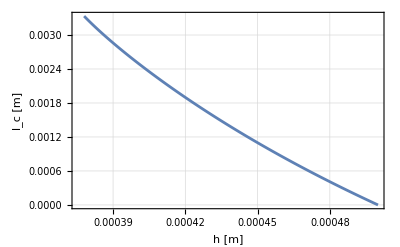

```mathematica
ListPlot[Transpose@{geom0[[1]],geom0[[2]]},FrameLabel->{"h [m]", "l_c [m]"},Joined->True,Evaluate@opts]
```

```mathematica
data0test={h0-> 0.5 10^-3,l0->0.5 10^-2};
```

```mathematica
h0range=h0{0.5,1,1.5}/.data0test//N;
l0range=l0{0.5,1,1.5}/.data0test//N;
h0strings=Table[StringJoin["h_0 = ",scientstring[h0range[[i]],3]," [m]"],{i,1,Length@h0range}]
l0strings=Table[StringJoin["l_0 = ",scientstring[l0range[[i]],3]," [m]"],{i,1,Length@l0range}]
```

{h_0 = 2.5×10^-4 [m],h_0 = 5.×10^-4 [m],h_0 = 7.5×10^-4 [m]}

{l_0 = 2.5×10^-3 [m],l_0 = 5.×10^-3 [m],l_0 = 7.5×10^-3 [m]}

```mathematica
geomhl=Table[solvegeom[h0range[[i]],l0range[[j]]],{i,1,Length@h0range},{j,1,Length@l0range}];(*geomhl[[i,j]] -> h0range[[i]],l0range[[j]]*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Manipulate[GraphicsGrid[{
Table[Block[{lim=l0range[[1]]},Show[Graphics[{White,Line[{{0,-lim},{0,lim}}],Black,Line[{{-lim,0},{lim,0}}]}],DrawCell[geomhl[[i,1]],idx,0],PlotLabel->Column[{h0strings[[i]],l0strings[[1]]}],LabelStyle->{Black,Bold},Axes->True]],{i,1,3}],
Table[Block[{lim=l0range[[2]]},Show[Graphics[{White,Line[{{0,-lim},{0,lim}}],Black,Line[{{-lim,0},{lim,0}}]}],DrawCell[geomhl[[i,2]],idx,0],PlotLabel->Column[{h0strings[[i]],l0strings[[2]]}],LabelStyle->{Black,Bold},Axes->True]],{i,1,3}],Table[Block[{lim=l0range[[3]]},Show[Graphics[{White,Line[{{0,-lim},{0,lim}}],Black,Line[{{-lim,0},{lim,0}}]}],DrawCell[geomhl[[i,3]],idx,0],PlotLabel->Column[{h0strings[[i]],l0strings[[3]]}],LabelStyle->{Black,Bold},Axes->True]],{i,1,3}]
},ImageSize->700],{idx,1,100,1,ControlPlacement->{Left,Bottom}}];
```

### Double cell unit

```mathematica
cell=geomhl[[3,3]];
hvec=cell[[1]];lcvec=cell[[2]];Rvec=cell[[3]];θvec=cell[[4]];
data0={h0->h0range[[3]],l0->l0range[[3]]};
```

```mathematica
Manipulate[Block[{lim=l0range[[3]],tf0=tf0/.celldata},
Show[
Table[DrawCell[cell,idx,{0,2(i-1)(hvec[[idx]]+tf0)},0],{i,1,2}],
PlotLabel->Row[{h0strings[[3]]," ",l0strings[[3]]}],LabelStyle->{Black,Bold},Axes->True,ImageSize->700,PlotRange->{{-l0/.data0,l0/.data0},{-1.5h0/.data0,4h0/.data0}}]],{idx,1,100,1}]
```

```mathematica
numdlch=Differences[lcvec]/Differences[hvec];
```

```mathematica
hveceff=hvec[[1;;Length@numdlch]];
```

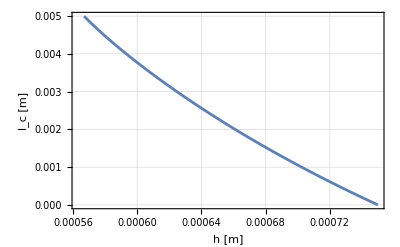
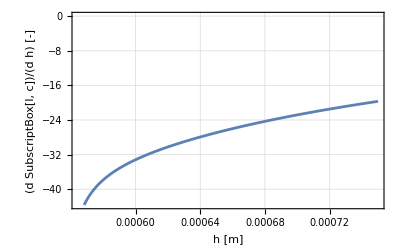

```mathematica
Row[{
ListPlot[Transpose[{hvec,lcvec}],Joined->True,Evaluate@opts,FrameLabel->{"h [m]","l_c [m]"}],
ListPlot[Transpose[{hveceff,numdlch}],Joined->True,Evaluate@opts,FrameLabel->{"h [m]","(d SubscriptBox[l, c])/(d h) [-]"}]}]
```

```mathematica
CC=(ϵp w0 lc[h])/(2 tp0);
```

```mathematica
dCCh=D[CC,h]
```

(w0 ϵp lc'[h])/(2 tp0)

```mathematica
F=-V^2/2 D[CC,h];
```

```mathematica
Fcell=F/.lc'[h]->numdlch/.celldata;
```

```mathematica
Vrange=Range[0,6000,2000];
Vstrings=Table[StringJoin["V = ",scientstring[Vrange[[i]],3]," [V]"],{i,1,Length@Vrange}];
```

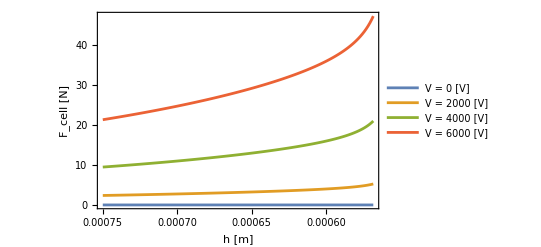

```mathematica
ListPlot[Table[Transpose[{hveceff,Fcell/.V->Vrange[[i]]}],{i,1,Length@Vrange}],ScalingFunctions->{"Reverse",Automatic},Joined->True,Evaluate@opts,FrameLabel->{"h [m]","F_cell [N]"},PlotLegends->Vstrings]
```

```mathematica
hdom=intFVmax["Domain"]//Flatten;
```

```mathematica
UelFh=CumTrapz[hvec[[1;;Length@Fcell]],Fcell/.V->6000];
```

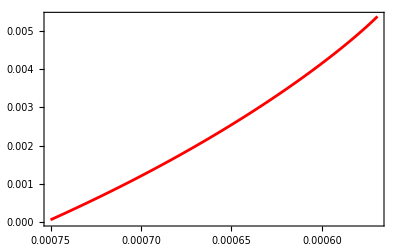

```mathematica
ListPlot[Transpose[{hveceff[[1;;Length@UelFh]],UelFh}],Joined->True,ScalingFunctions->{"Reverse",Automatic},Evaluate@opts]
```

### Stack

```mathematica
Ns=5;
```

```mathematica
Manipulate[Block[{lim=l0range[[3]],tf0=10^-5,Ns=5,Nc=3},
Show[Table[DrawCell[cell,idx,{(j-2) l0range[[3]],2(i-1)(hvec[[idx]]+tf0)},0],{j,1,Nc},{i,1,Ns}],
PlotLabel->Row[{h0strings[[3]]," ",l0strings[[3]]}],LabelStyle->{Black,Bold},Axes->True,ImageSize->1000,PlotRange->{Nc/2{-l0/.data0,l0/.data0},{-1.5h0/.data0,2Ns h0/.data0}}]]
,{idx,1,100,1}]
```